```mathematica
(*Non dimensionalize using lref = 1/β and tref = tf*)
(*for atmosphere,1/β is approximately 8 km, so for xf is 5000km, xf_nonD is approximately 600*)
```

```mathematica
eqn1=u1'[t] == u1[t] u2[t]
eqn2=u2'[t] == (1/2)(u2[t]^2 - u1[t]^2)
```

u1'[t]==u1[t] u2[t]

u2'[t]==1/2 (-u1[t]^2+u2[t]^2)

```mathematica
diffeqSol=(DSolve[{eqn1,eqn2},{u1[t], u2[t]},{t}]//FullSimplify)/.{C[1]-> c1, C[2]-> c2}
```

{{u2[t]→-2 √((c1^4 (-c2+t)^2)/((4+c1^2 (-c2+t)^2)^2)),u1[t]→(4 c1)/(4+c1^2 (-c2+t)^2)},{u2[t]→2 √((c1^4 (c2+t)^2)/((4+c1^2 (c2+t)^2)^2)),u1[t]→(4 c1)/(4+c1^2 (c2+t)^2)}}

```mathematica
u11sol=u1[t]/.diffeqSol[[1]]
u21sol=u2[t]/.diffeqSol[[1]]
u12sol=u1[t]/.diffeqSol[[2]]
u22sol=u2[t]/.diffeqSol[[2]]
```

(4 c1)/(4+c1^2 (-c2+t)^2)

-2 √((c1^4 (-c2+t)^2)/((4+c1^2 (-c2+t)^2)^2))

(4 c1)/(4+c1^2 (c2+t)^2)

2 √((c1^4 (c2+t)^2)/((4+c1^2 (c2+t)^2)^2))

```mathematica
u21sol=Assuming[t>0 && c1>0 && c2>0,Refine[u21sol]]
```

-(2 c1^2 Abs[-c2+t])/(4+c1^2 (-c2+t)^2)

```mathematica
u22sol=Assuming[t>0 && c1>0 && c2>0,Refine[u22sol]]
```

(2 c1^2 (c2+t))/(4+c1^2 (c2+t)^2)

```mathematica
(*Since the second solution has positive hdot, we use that as the first half of the solution*)
```

```mathematica
(*Boundary conditions are that the integral of u1 is xf, and integral of u2 is 0, integrals are from 0 to 1*)
```

```mathematica
exp1=(Integrate[u12sol,{t,0,1/2},Assumptions->{c1>0, c2>0}]) + (Integrate[u11sol,{t,1/2,1},Assumptions->{c1>0, c2>0}])//FullSimplify
```

-2 (ArcTan[1/2 c1 (-1+c2)]+ArcTan[(c1 c2)/2]-ArcTan[1/4 c1 (1+2 c2)]+ArcTan[1/4 (c1-2 c1 c2)])

```mathematica
exp2=Integrate[u22sol,{t,0,1/2},Assumptions->{c1>0, c2>0}] +Integrate[u21sol,{t,1/2,1},Assumptions->{c1>0, c2>0}]//FullSimplify
```

Log[(16+(c1+2 c1 c2)^2)/(4 (4+c1^2 c2^2))]+(Piecewise[{{Log[64]+Log[1/(4+c1^2 (-1+c2)^2)]+Log[1/(16+c1^2 (-1+2 c2)^2)], 1/2<c2≤1}, {Log[(4 (4+c1^2 (-1+c2)^2))/(16+c1^2 (-1+2 c2)^2)], c2>1||c2≤0}, {Log[(16+c1^2 (-1+2 c2)^2)/(4 (4+c1^2 (-1+c2)^2))], True}}])

```mathematica
exp1==xf
```

-2 (ArcTan[1/2 c1 (-1+c2)]+ArcTan[(c1 c2)/2]-ArcTan[1/4 c1 (1+2 c2)]+ArcTan[1/4 (c1-2 c1 c2)])==xf

```mathematica
exp2==0
```

Log[(16+(c1+2 c1 c2)^2)/(4 (4+c1^2 c2^2))]+(Piecewise[{{Log[64]+Log[1/(4+c1^2 (-1+c2)^2)]+Log[1/(16+c1^2 (-1+2 c2)^2)], 1/2<c2≤1}, {Log[(4 (4+c1^2 (-1+c2)^2))/(16+c1^2 (-1+2 c2)^2)], c2>1||c2≤0}, {Log[(16+c1^2 (-1+2 c2)^2)/(4 (4+c1^2 (-1+c2)^2))], True}}])==0

```mathematica
Assuming[c1>0 && c2>0,Solve[Log[(16+(c1+2 c1 c2)^2)/(4 (4+c1^2 c2^2))]+Piecewise[{{Log[64]+Log[1/(4+c1^2 (-1+c2)^2)]+Log[1/(16+c1^2 (-1+2 c2)^2)],1/2<c2≤1},{Log[(4 (4+c1^2 (-1+c2)^2))/(16+c1^2 (-1+2 c2)^2)],c2>1||c2≤0}},Log[(16+c1^2 (-1+2 c2)^2)/(4 (4+c1^2 (-1+c2)^2))]]==0,c1]]
```

```mathematica
Length[%159]
```

13

```mathematica
%159[[1]]
```

{c1→ConditionalExpression[0,0<c2<1/4||1/4<c2≤1/2]}

```mathematica
%159[[4]][[1]][[2]][[1]]
```

-4 √(1/(-1-2 c2+4 c2^2))+ⅈ Root[256/((-1-2 c2+4 c2^2)^2)+(512 c2)/((-1-2 c2+4 c2^2)^2)-(1024 c2^2)/((-1-2 c2+4 c2^2)^2)+256/(-1-2 c2+4 c2^2)+(-16-96/(-1-2 c2+4 c2^2)-(192 c2)/(-1-2 c2+4 c2^2)+(384 c2^2)/(-1-2 c2+4 c2^2)) #1^2+(1+2 c2-4 c2^2) #1^4&,2]

```mathematica
Reduce[exp1,{c1,c2},Reals]
```

Reduce[-2 (ArcTan[1/2 c1 (-1+c2)]+ArcTan[(c1 c2)/2]-ArcTan[1/4 c1 (1+2 c2)]+ArcTan[1/4 (c1-2 c1 c2)]),{c1,c2},Reals]

```mathematica
exp1
```

-2 (ArcTan[1/2 c1 (-1+c2)]+ArcTan[(c1 c2)/2]-ArcTan[1/4 c1 (1+2 c2)]+ArcTan[1/4 (c1-2 c1 c2)])

```mathematica
exp2
```

Log[(16+(c1+2 c1 c2)^2)/(4 (4+c1^2 c2^2))]+(Piecewise[{{Log[64]+Log[1/(4+c1^2 (-1+c2)^2)]+Log[1/(16+c1^2 (-1+2 c2)^2)], 1/2<c2≤1}, {Log[(4 (4+c1^2 (-1+c2)^2))/(16+c1^2 (-1+2 c2)^2)], c2>1||c2≤0}, {Log[(16+c1^2 (-1+2 c2)^2)/(4 (4+c1^2 (-1+c2)^2))], True}}])

```mathematica
rules=FindRoot[{exp1== 50,exp2==0},{{c1,1},{c2,1}}]
```

{c1→136949.,c2→-0.422982}

```mathematica
If[tp<1/2, NIntegrate[u12sol,{t,0,tp}], NIntegrate[u12sol,{t,0,1/2 }] + NIntegrate[u11sol,{t,1/2,tp}]]/.rules/.tp-> 0.25
```

NIntegrate[u12sol,{t,0,0.25}]

```mathematica
NIntegrate[u12sol,{t,0,0.25}]
```

NIntegrate[u12sol,{t,0,0.25}]

```mathematica
u12sol/.rules
```

547796./(4+1.8755×10^10 (-0.422982+t)^2)

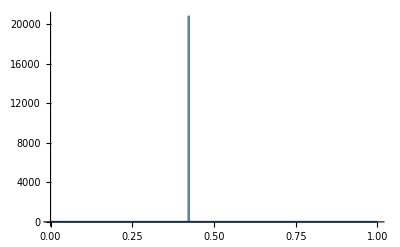

```mathematica
g1=Plot[u12sol/.rules,{t,0,0.5},PlotRange->Full];
g2=Plot[u11sol/.rules,{t,0.5,1}];
Show[{g1,g2},PlotRange-> {{0,1},Automatic}]
```

```mathematica
Assuming[c1>0,Integrate[(u11sol/.c2-> 0),{t,0,1}]]==xf
```

2 ArcTan[c1/2]==xf

```mathematica
Assuming[xf>0&& Im[xf]==0,Solve[2 ArcTan[c1/2]==xf,{c1}]]
```

{{c1→ConditionalExpression[2 Tan[xf/2],(-π≤Re[xf]<π&&Im[xf]<0)||-π<Re[xf]<π||(-π<Re[xf]≤π&&Im[xf]>0)]}}

```mathematica
c1-> 2 Tan[xf/2]
```

c1→2 Tan[xf/2]

```mathematica
u11sol/.{c2-> 0,c1->2 Tan[xf/2]}//FullSimplify
```

(2 Tan[xf/2])/(1+t^2 Tan[xf/2]^2)

```mathematica
Assuming[xf>0&&t>0,Refine[u22sol/.{c2-> 0,c1->2 Tan[xf/2]}]//FullSimplify]
```

2 t √(Tan[xf/2]^4/((1+t^2 Tan[xf/2]^2)^2))

```mathematica
Manipulate[Plot[ {2 t √(Tan[xf/2]^4/((1+t^2 Tan[xf/2]^2)^2)),-2 t √(Tan[xf/2]^4/((1+t^2 Tan[xf/2]^2)^2))},{t,0,1}],{xf,0.5,100}]
```

```mathematica
u21sol
u22sol
```

-2 √((c1^4 (-c2+t)^2)/((4+c1^2 (-c2+t)^2)^2))

2 √((c1^4 (c2+t)^2)/((4+c1^2 (c2+t)^2)^2))

```mathematica
p1=(Integrate[u22sol,t]/.t-> ts)-(Integrate[u22sol,t]/.t-> 0)
```

-(√((c1^4 c2^2)/((4+c1^2 c2^2)^2)) (4+c1^2 c2^2) Log[4+c1^2 c2^2])/(c1^2 c2)+(√((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) (4+c1^2 (c2+ts)^2) Log[4+c1^2 (c2+ts)^2])/(c1^2 (c2+ts))

```mathematica
p2=(Integrate[u21sol,t]/.t-> 1)-(Integrate[u21sol,t]/.t-> ts)
```

((4+c1^2 (-1+c2)^2) √((c1^4 (-1+c2)^2)/((4+c1^2 (-1+c2)^2)^2)) Log[4+c1^2 (-1+c2)^2])/(c1^2 (-1+c2))-((4+c1^2 (c2-ts)^2) √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) Log[4+c1^2 (c2-ts)^2])/(c1^2 (c2-ts))

```mathematica
Together[p1+p2]//Numerator
```

4 c2^3 √((c1^4 (-1+c2)^2)/((4+c1^2-2 c1^2 c2+c1^2 c2^2)^2)) Log[4+c1^2 (-1+c2)^2]+c1^2 c2^3 √((c1^4 (-1+c2)^2)/((4+c1^2-2 c1^2 c2+c1^2 c2^2)^2)) Log[4+c1^2 (-1+c2)^2]-2 c1^2 c2^4 √((c1^4 (-1+c2)^2)/((4+c1^2-2 c1^2 c2+c1^2 c2^2)^2)) Log[4+c1^2 (-1+c2)^2]+c1^2 c2^5 √((c1^4 (-1+c2)^2)/((4+c1^2-2 c1^2 c2+c1^2 c2^2)^2)) Log[4+c1^2 (-1+c2)^2]-4 c2 √((c1^4 (-1+c2)^2)/((4+c1^2-2 c1^2 c2+c1^2 c2^2)^2)) ts^2 Log[4+c1^2 (-1+c2)^2]-c1^2 c2 √((c1^4 (-1+c2)^2)/((4+c1^2-2 c1^2 c2+c1^2 c2^2)^2)) ts^2 Log[4+c1^2 (-1+c2)^2]+2 c1^2 c2^2 √((c1^4 (-1+c2)^2)/((4+c1^2-2 c1^2 c2+c1^2 c2^2)^2)) ts^2 Log[4+c1^2 (-1+c2)^2]-c1^2 c2^3 √((c1^4 (-1+c2)^2)/((4+c1^2-2 c1^2 c2+c1^2 c2^2)^2)) ts^2 Log[4+c1^2 (-1+c2)^2]+4 c2^2 √((c1^4 c2^2)/((4+c1^2 c2^2)^2)) Log[4+c1^2 c2^2]-4 c2^3 √((c1^4 c2^2)/((4+c1^2 c2^2)^2)) Log[4+c1^2 c2^2]+c1^2 c2^4 √((c1^4 c2^2)/((4+c1^2 c2^2)^2)) Log[4+c1^2 c2^2]-c1^2 c2^5 √((c1^4 c2^2)/((4+c1^2 c2^2)^2)) Log[4+c1^2 c2^2]-4 √((c1^4 c2^2)/((4+c1^2 c2^2)^2)) ts^2 Log[4+c1^2 c2^2]+4 c2 √((c1^4 c2^2)/((4+c1^2 c2^2)^2)) ts^2 Log[4+c1^2 c2^2]-c1^2 c2^2 √((c1^4 c2^2)/((4+c1^2 c2^2)^2)) ts^2 Log[4+c1^2 c2^2]+c1^2 c2^3 √((c1^4 c2^2)/((4+c1^2 c2^2)^2)) ts^2 Log[4+c1^2 c2^2]+4 c2^2 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) Log[4+c1^2 (c2-ts)^2]-4 c2^3 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) Log[4+c1^2 (c2-ts)^2]+c1^2 c2^4 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) Log[4+c1^2 (c2-ts)^2]-c1^2 c2^5 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) Log[4+c1^2 (c2-ts)^2]+4 c2 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) ts Log[4+c1^2 (c2-ts)^2]-4 c2^2 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) ts Log[4+c1^2 (c2-ts)^2]-c1^2 c2^3 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) ts Log[4+c1^2 (c2-ts)^2]+c1^2 c2^4 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) ts Log[4+c1^2 (c2-ts)^2]-c1^2 c2^2 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) ts^2 Log[4+c1^2 (c2-ts)^2]+c1^2 c2^3 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) ts^2 Log[4+c1^2 (c2-ts)^2]+c1^2 c2 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) ts^3 Log[4+c1^2 (c2-ts)^2]-c1^2 c2^2 √((c1^4 (c2-ts)^2)/((4+c1^2 (c2-ts)^2)^2)) ts^3 Log[4+c1^2 (c2-ts)^2]-4 c2^2 √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]+4 c2^3 √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]-c1^2 c2^4 √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]+c1^2 c2^5 √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]+4 c2 ts √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]-4 c2^2 ts √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]-c1^2 c2^3 ts √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]+c1^2 c2^4 ts √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]+c1^2 c2^2 ts^2 √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]-c1^2 c2^3 ts^2 √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]+c1^2 c2 ts^3 √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]-c1^2 c2^2 ts^3 √((c1^4 (c2+ts)^2)/((4+c1^2 (c2+ts)^2)^2)) Log[4+c1^2 (c2+ts)^2]

```mathematica
diffeqSol=(DSolve[{eqn1,eqn2},{u1[t], u2[t]},{t}]//FullSimplify)
```

{{u2[t]→-2 √((C[1]^4 (t-C[2])^2)/((4+C[1]^2 (t-C[2])^2)^2)),u1[t]→(4 C[1])/(4+C[1]^2 (t-C[2])^2)},{u2[t]→2 √((C[1]^4 (t+C[2])^2)/((4+C[1]^2 (t+C[2])^2)^2)),u1[t]→(4 C[1])/(4+C[1]^2 (t+C[2])^2)}}

```mathematica
bc1 = Integrate[u1[t],{t,0,1}]== xf
bc2 = Integrate[u2[t],{t,0,1}] == 0
```

∫_0^1 u1[t]ⅆt==xf

∫_0^1 u2[t]ⅆt==0

```mathematica
NDSolve[{eqn1,eqn2,bc1,bc2},{u1[t], u2[t]},{t,0,1}]
```

NDSolve[{u1'[t]==u1[t] u2[t],u2'[t]==1/2 (-u1[t]^2+u2[t]^2),∫_0^1 u1[t]ⅆt==xf,∫_0^1 u2[t]ⅆt==0},{u1[t],u2[t]},{t,0,1}]

```mathematica
e1=x''[t] == x'[t] h'[t]
e2=h''[t] == 1/2(h'[t]^2 - x'[t]^2)
b1=x[0] == 0
b2=x[1] == xf
b3=h[0]== 0
b4=h[1]==0
eqns={e1,e2,b1,b2,b3,b4}
```

x''[t]==h'[t] x'[t]

h''[t]==1/2 (h'[t]^2-x'[t]^2)

x[0]==0

x[1]==xf

h[0]==0

h[1]==0

{x''[t]==h'[t] x'[t],h''[t]==1/2 (h'[t]^2-x'[t]^2),x[0]==0,x[1]==xf,h[0]==0,h[1]==0}

```mathematica
sol=NDSolve[eqns/.xf->0.5,{x[t],h[t]},{t,0,1}]
```

{{x[t]→InterpolatingFunction[{{0., 1.}}, <>][t],h[t]→InterpolatingFunction[{{0., 1.}}, <>][t]}}

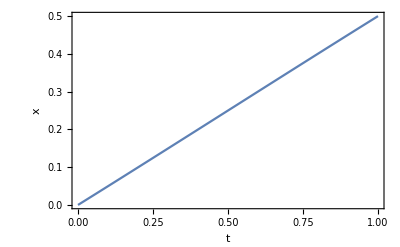

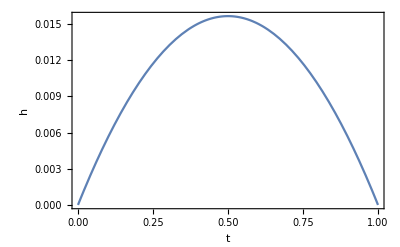

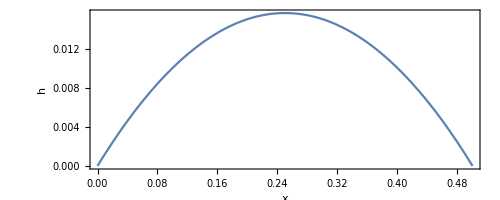

```mathematica
Plot[(x[t]/.sol)[[1]],{t,0,1},Frame-> True,FrameLabel->{"t","x"}]
Plot[(h[t]/.sol)[[1]],{t,0,1},Frame-> True,FrameLabel->{"t","h"}]
ParametricPlot[{(x[t]/.sol)[[1]],(h[t]/.sol)[[1]]},{t,0,1},Frame-> True,FrameLabel->{"x","h"}]
```

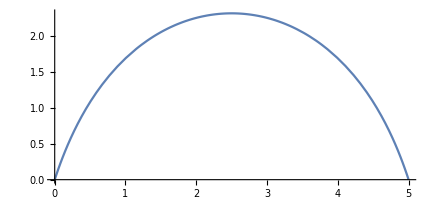

```mathematica
ParametricPlot[{(x[t]/.sol)[[1]],(h[t]/.sol)[[1]]},{t,0,1}]
```